4 x^3

nsr = ϕ^2/12

x→26.8328

0.149071

{{ϕ→InterpolatingFunction[{{0.,60.}},<>]}}

{26.8328}

{30.8795}

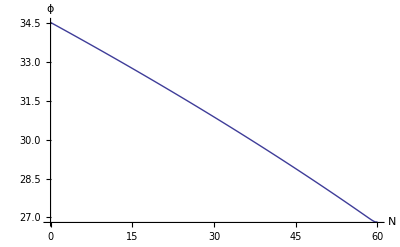

```mathematica
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
(* Define a potential *)
(*v[x_] := x^4*(1-Log[x])*)
v[x_] := x^4
vp[x_]=v'[x]
(* Define H as a function of number of efolds *)
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))]
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2)
(* Define number of efolds using slow-roll approx *)
nsr[x_] := v[x]/v''[x]
Print["nsr = ",nsr[ϕ]]
(* find ϕ60, ϕ at n=60 *)
ϕ60 = Evaluate[Last[FindRoot[{nsr[x]-60==0},{x,1}]]]
(* find ϕp60 = ϕ'[60] *)
ϕp60 = v'[x]/v[x]/.ϕ60 
(* Solve for ϕ[n] *)
ϕsol = NDSolve[{6*hsq[n]*ϕ''[n]+3*vp[ϕ[n]]*(ϕ'[n])^2+6*hsq[n]*((ϕ'[n])^3-3*ϕ'[n])-6*v'[ϕ[n]]==0,(x/.ϕ60)==ϕ[60],ϕp60==ϕ'[60]},ϕ,{n,60,0}]
ϕ[60]/.ϕsol
ϕ[30]/.ϕsol
Plot[Evaluate[ϕ[n]/.ϕsol],{n,60,0},AxesLabel->{N,ϕ}]
```

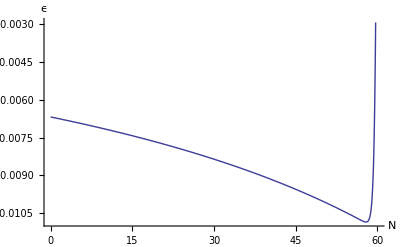

```mathematica
(* Find ϵ[n] *)
ϵ[n_] := 1/2*D[Log[v[ϕ[n]/.ϕsol]],n]
Plot[Evaluate[ϵ[n]],{n,60,0},AxesLabel->{N,ϵ}]
```

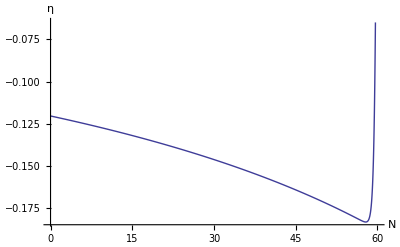

```mathematica
(* Find η[n] *)
ϕp[x_] := v'[x]/v[x]
η[n_] := 1/2*D[Log[vp[ϕ[n]/.ϕsol]]^2,n]
Plot[Evaluate[η[n]],{n,60,0},AxesLabel->{N,η}]
```